# Exploring different forms of Gene drive. Diploid selection for n loci p allele model

## Modules

Conversions

```mathematica
GametestoGenotypes[Fgametes_]:=Block[{out=ConstantArray[0,Length[Genotypes]],Gamete1,Gamete2,position1,position2},
For[i=1,i≤Length[Genotypes],++i,
Gamete1=Genotypes[[i]][[1]];
Gamete2=Genotypes[[i]][[2]];
position1=Position[Gametes,Gamete1][[1,1]];
position2=Position[Gametes,Gamete2][[1,1]];
out[[i]]=Fgametes[[position1]]*Fgametes[[position2]];
];
out
]
```

```mathematica
GenotypetoGametes[FGenotypes_]:=Block[{out=ConstantArray[0,Length[Gametes]],Gamete1,Gamete2,position1,position2},
For[i=1,i≤Length[FGenotypes],++i,
Gamete1=Genotypes[[i]][[1]];
Gamete2=Genotypes[[i]][[2]];
position1=Position[Gametes,Gamete1][[1,1]];
position2=Position[Gametes,Gamete2][[1,1]];
out[[position1]]+=1/2 FGenotypes[[i]];
out[[position2]]+=1/2 FGenotypes[[i]];
];
out
]
```

Recombination

```mathematica
Clear[GameteRecombinants]
GameteRecombinants[ga1_,ga2_,Gametes_,Loci_]:=Block[{out={},rec,i},
rec=Tuples[{ga1,ga2},Length[Loci]];
For[i=1,i≤Length[rec],++i,
AppendTo[out,Table[Gametes[[rec[[i]][[j]]]][[j]],{j,1,Length[Loci]}]]
];
out
]
```

```mathematica
Recombination[Fgametes_,Gametes_,Loci_]:=Block[{out=ConstantArray[0,Length[Fgametes]],i,j},
(*For each interaction, what is the contribution by recombination to the frequency of diploid genotypes*)
(*Assuming free recombination*)
For[i=1,i≤Length[Fgametes],++i,
For[j=1,j≤Length[Fgametes],++j,
Do[out[[Position[Gametes,k][[1,1]]]]+=Fgametes[[i]]Fgametes[[j]] 1/2^Length[Loci],{k,GameteRecombinants[i,j,Gametes,Loci]}];
];
];
out
]
```

Meiotic drive

```mathematica
(*Linear operators so can be written in matrix form*)
(*The transgenic alleles are expressed in the germline cells of the offspring*)
(*Need a conversion list like: {converts genotype1->haplotype2} (assuming frequency h). They can be summarized as doubles (h1,h2)*)
```

```mathematica
Clear[MakeTransitionMatrix]
MakeTransitionMatrix[ConversionList_]:=Block[{i,From,To,TransitionMeitotic=IdentityMatrix[Length[Genotypes]]},
Assert[CountDistinct[ConversionList[[;;,1]]]==Length[ConversionList[[;;,1]]]];
For[i=1,i≤Length[ConversionList],++i,
From=Position[Genotypes,ConversionList[[i]][[1]]][[1,1]];
To=Position[Genotypes,ConversionList[[i]][[2]]][[1,1]];
TransitionMeitotic[[From,From]]=1-ConversionList[[i]][[3]];
TransitionMeitotic[[To,From]]=ConversionList[[i]][[3]];
];
TransitionMeitotic
]
```

```mathematica
MeioticDrive[Fgametes_,TransitionMatrix_]:=Block[{genotypes},
(*turn to genotypes assuming HWE*)
genotypes=GametestoGenotypes[Fgametes];
genotypes=TransitionMatrix.genotypes;
GenotypetoGametes[genotypes]
]
```

Diploid Selection

```mathematica
DiploidSelection[Fgametes_,W_,Genotypes_,Gametes_]:=
Block[{i,j,out=ConstantArray[0,Length[Fgametes]]},
For[i=1,i≤Length[Fgametes],++i,
For[j=1,j≤Length[Fgametes],++j,
out[[i]]+=Fgametes[[i]] Fgametes[[j]] W[[Position[Genotypes,{Gametes[[i]],Gametes[[j]]}][[1,1]]]]
];
];
out/Total[out]
]
```

Mutation

```mathematica
(*Linear operators so can be written in matrix form*)
```

```mathematica
Clear[MakeMutationMatrix]
MakeMutationMatrix[ConversionList_]:=Block[{i,From,To,TransitionMeitotic=IdentityMatrix[Length[Gametes]]},
Assert[CountDistinct[ConversionList[[;;,1]]]==Length[ConversionList[[;;,1]]]];
For[i=1,i≤Length[ConversionList],++i,
From=Position[Gametes,ConversionList[[i]][[1]]][[1,1]];
To=Position[Gametes,ConversionList[[i]][[2]]][[1,1]];
(*Assert[Abs[ConversionList[[i]][[3]]]≤1];*)
TransitionMeitotic[[To,From]]=ConversionList[[i]][[3]];
];
For[i=1,i≤Length[ConversionList],++i,
TransitionMeitotic[[i,i]]=2-Total[TransitionMeitotic[[;;,i]]];
];
TransitionMeitotic
]
```

```mathematica
Mutation[Fgametes_,TransitionMatrix_]:=Block[{genotypes},
(*turn to genotypes assuming HWE*)
TransitionMatrix.Fgametes
]
```

Subset dataset

```mathematica
SubsetData[critical_,data_,Gametes_]:=Block[{out={}},
For[i=1,i≤Length[Gametes],++i,
If[Max[data[[;;,i]]]≥critical,
AppendTo[out,data[[;;,i]]];
]
];
out]
```

## Numerical Analyses

Numerical Analysis of 1 locus Under-dominance

## Model

```mathematica
(*Set environmental variables*)
Loci={{"A0","A1","A2"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
On[Assert]
```

```mathematica
Clear[F];
F[t_]:=F[t]=DiploidSelection[Recombination[F[t-1],Gametes,Loci],W,Genotypes,Gametes]
```

## Dynamics

```mathematica
(*Initial conditions*)
W=ConstantArray[0,Length[Genotypes]]; 
W[[1]]=1;
W[[6]]=1-0.2;
W[[8]]=1-0.2;

Clear[F]
F[t_]:=F[t]=DiploidSelection[Recombination[F[t-1],Gametes,Loci],W,Genotypes,Gametes]
F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];
Assert[Length[F0]==Length[Gametes]]
Assert[Total[F0]==1]
F[0]=F0;
```

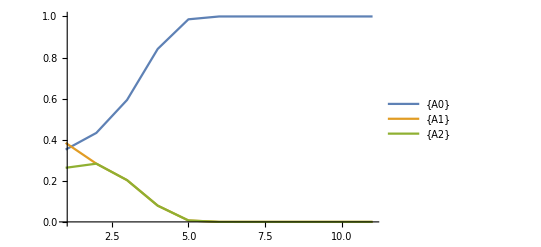

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,10}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->{ToString[Gametes[[1]]],ToString[Gametes[[2]]],ToString[Gametes[[3]]]}]
```

```mathematica
Clear[W,F0]
```

## Equilibria

```mathematica
W=ConstantArray[0,Length[Genotypes]]; 
W[[1]]=1;
W[[6]]=1-s;
W[[8]]=1-s;

DiploidSelection[Recombination[{F1,F2,F3},Gametes,Loci],W,Genotypes,Gametes]//FullSimplify
```

{F1^2/(F1^2-2 F2 F3 (-1+s)),(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s)),(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s))}

```mathematica
Solve[{F1==F1^2/(F1^2-2 F2 F3 (-1+s)),F2==(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s)),F3==(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s))},{F1,F2,F3}]//FullSimplify
```

{{F1→1,F2→0,F3→0},{F1→0,F2→1/2,F3→1/2},{F1→1+2/(-3+s),F2→1/(3-s),F3→1/(3-s)}}

## Local Stability Analysis

```mathematica
(*Evaluate the Jacobian  local stability matrix *)
```

```mathematica
F1prime[F1_,F2_,F3_]:=F1^2/(F1^2-2 F2 F3 (-1+s));
F2prime[F1_,F2_,F3_]:=(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s));
F3prime[F1_,F2_,F3_]:=(F2 F3 (-1+s))/(-F1^2+2 F2 F3 (-1+s));
```

```mathematica
StabilityMatrix={{D[F1prime[F1,F2,F3],F1],D[F1prime[F1,F2,F3],F2],D[F1prime[F1,F2,F3],F3]},
{D[F2prime[F1,F2,F3],F1],D[F1prime[F1,F2,F3],F2],D[F2prime[F1,F2,F3],F3]},
{D[F3prime[F1,F2,F3],F1],D[F1prime[F1,F2,F3],F2],D[F3prime[F1,F2,F3],F3]}
}
```

{{-(2 F1^3)/((F1^2-2 F2 F3 (-1+s))^2)+(2 F1)/(F1^2-2 F2 F3 (-1+s)),(2 F1^2 F3 (-1+s))/((F1^2-2 F2 F3 (-1+s))^2),(2 F1^2 F2 (-1+s))/((F1^2-2 F2 F3 (-1+s))^2)},{(2 F1 F2 F3 (-1+s))/((-F1^2+2 F2 F3 (-1+s))^2),(2 F1^2 F3 (-1+s))/((F1^2-2 F2 F3 (-1+s))^2),(F2 (-1+s))/(-F1^2+2 F2 F3 (-1+s))-(2 F2^2 F3 (-1+s)^2)/((-F1^2+2 F2 F3 (-1+s))^2)},{(2 F1 F2 F3 (-1+s))/((-F1^2+2 F2 F3 (-1+s))^2),(2 F1^2 F3 (-1+s))/((F1^2-2 F2 F3 (-1+s))^2),(F2 (-1+s))/(-F1^2+2 F2 F3 (-1+s))-(2 F2^2 F3 (-1+s)^2)/((-F1^2+2 F2 F3 (-1+s))^2)}}

```mathematica
Eigen=Solve[Det[StabilityMatrix-λ IdentityMatrix[3]]==0,λ]//FullSimplify
```

{{λ→0},{λ→-((F1 (F1 (F2-2 F3)+4 F2 F3+√(F1^2 (F2-2 F3)^2+16 F2^2 F3^2+8 F1 F2 F3 (F2+4 F3))) (-1+s))/(2 (F1^2-2 F2 F3 (-1+s))^2))},{λ→(F1 (-F1 F2+2 F1 F3-4 F2 F3+√(F1^2 (F2-2 F3)^2+16 F2^2 F3^2+8 F1 F2 F3 (F2+4 F3))) (-1+s))/(2 (F1^2-2 F2 F3 (-1+s))^2)}}

### Stability of {F1→1,F2→0,F3→0}

```mathematica
Eigen/.{F1->1,F2->0,F3->0}
```

{{λ→0},{λ→0},{λ→0}}

All eigenvalues are less than 1 so this equilibrium is locally stable

### Stability of {F1→0,F2→1/2,F3→1/2}

```mathematica
Eigen/.{F1->0,F2->1/2,F3->1/2}
```

{{λ→0},{λ→0},{λ→0}}

All eigenvalues are less than 1 so this equilibrium is locally stable

### Stability of {F1→1+2/(-3+s),F2→1/(3-s),F3→1/(3-s)}

```mathematica
Eigen/.{F1->1+2/(-3+s),F2->1/(3-s),F3->1/(3-s)}//FullSimplify
```

{{λ→0},{λ→1/2 (-1-6/(-3+s)+3 √((57+(-42+s) s)/(-3+s)^4)-s √((57+(-42+s) s)/(-3+s)^4))},{λ→1/2 (-1-6/(-3+s)-3 √((57+(-42+s) s)/(-3+s)^4)+s √((57+(-42+s) s)/(-3+s)^4))}}

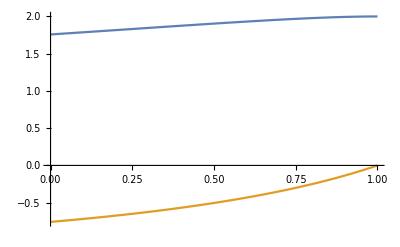

```mathematica
Plot[
{1/2 (-1-6/(-3+s)+3 √((57+(-42+s) s)/(-3+s)^4)-s √((57+(-42+s) s)/(-3+s)^4)),1/2 (-1-6/(-3+s)-3 √((57+(-42+s) s)/(-3+s)^4)+s √((57+(-42+s) s)/(-3+s)^4))},{s,0,1}]
```

Not all eigenvalues are less than 1. This equilibrium is locally unstable.

## Invasion plot

We call invasion when equilibrium {F1->1,F2->0,F3->0} is reached after 10 generations. Surely we can do a better job then this. Question: is there a way to analytically show where the threshold is (the equations are nonlinear..)

```mathematica
Clear[Finv];
Finv[t_,f1_,s_]:=Finv[t,f1,s]=DiploidSelection[Recombination[Finv[t-1,f1,s],Gametes,Loci],W,Genotypes,Gametes]
```

```mathematica
Equil[f1_,s_]:=Block[{out},
Finv[0,f1,s]={f1,(1-f1)/2,(1-f1)/2};
If[Chop[Finv[5,f1,s]][[1]]==1,1,0]
]
```

```mathematica
Data=Flatten[Table[{s,f1,Equil[f1,s]},{s,0,1,0.01},{f1,0.1,1,0.01}],1];
```

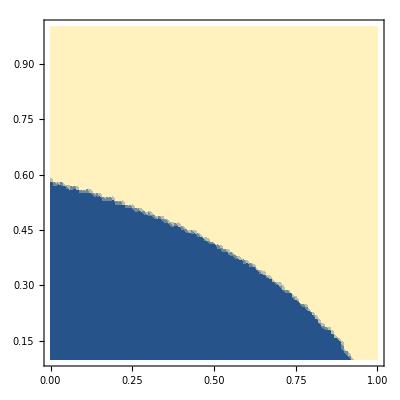

```mathematica
ListDensityPlot[Data]
```

Numerical Analysis of 2 locus Under-dominance

## Dynamics

```mathematica
On[Assert]
```

```mathematica
(*Set environmental variables*)
Loci={{"Aw","At"},{"Bw","Bt"}};
Gametes =Tuples[Loci]
Genotypes=Tuples[Gametes,2];
```

{{Aw,Bw},{Aw,Bt},{At,Bw},{At,Bt}}

```mathematica
(*Initial conditions*)
W=ConstantArray[ϵ,Length[Genotypes]]; 
W[[1]]=1;
W[[4]]=(1-s)^(1/2);
W[[7]]=(1-s)^(1/2);
W[[8]]=(1-s)^(1/2);
W[[10]]=(1-s)^(1/2);
W[[12]]=(1-s);
W[[13]]=(1-s)^(1/2);
W[[14]]=(1-s)^(1/2);
W[[15]]=(1-s);
W[[16]]=(1-s);
(*Same indexing as genotype*)
ArrayReshape[W,{4,4}]//MatrixForm
```

(1 | ϵ | ϵ | √(1-s)
ϵ | ϵ | √(1-s) | √(1-s)
ϵ | √(1-s) | ϵ | 1-s
√(1-s) | √(1-s) | 1-s | 1-s)

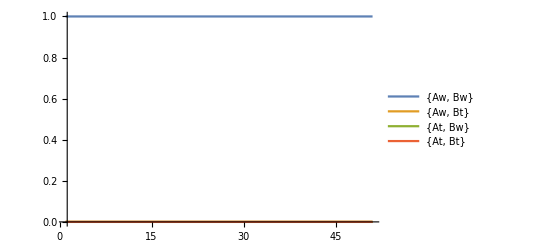

```mathematica
Clear[F]
F[t_]:=F[t]=DiploidSelection[Recombination[F[t-1],Gametes,Loci],W/.s->0.5,Genotypes,Gametes]
(*F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];*)
F0w=0.9;
F0={1,0,0,0};
Assert[Total[F0]==1];
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,50}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->{ToString[Gametes[[1]]],ToString[Gametes[[2]]],ToString[Gametes[[3]]],ToString[Gametes[[4]]]}]
```

## Equilibrium

```mathematica
Equations=DiploidSelection[Recombination[Table[P[i],{i,1,4}],Gametes,Loci],W,Genotypes,Gametes];
```

```mathematica
Equations/.{P[3]->0,P[2]->0,P[4]->0}
```

{1,0,0,0}

## Invasion plots

We call invasion when equilibrium {F1->1,F2->0,F3->0} is reached. Question: is there a way to analytically show where the threshold is (the equations are nonlinear..)

```mathematica
Clear[Finv];
Finv[t_,f1_,sel_]:=Finv[t,f1,sel]=DiploidSelection[Recombination[Finv[t-1,f1,sel],Gametes,Loci],W/.{s->sel},Genotypes,Gametes]
W=ConstantArray[0,Length[Genotypes]]; 
W[[1]]=1;
W[[4]]=(1-s)^(1/2);
W[[7]]=(1-s)^(1/2);
W[[8]]=(1-s)^(1/2);
W[[10]]=(1-s)^(1/2);
W[[12]]=(1-s);
W[[13]]=(1-s)^(1/2);
W[[14]]=(1-s)^(1/2);
W[[15]]=(1-s);
W[[16]]=(1-s);
```

```mathematica
Equil[f1_,s_]:=Block[{out},
Finv[0,f1,s]={(1-f1),0,0,f1};
out=1/2 Finv[100,f1,s][[2]]+Finv[50,f1,s][[4]]]
```

```mathematica
Data2=Flatten[Table[{s,f1,Equil[f1,s]},{s,0,1,0.05},{f1,0.1,1,0.05}],1];
```

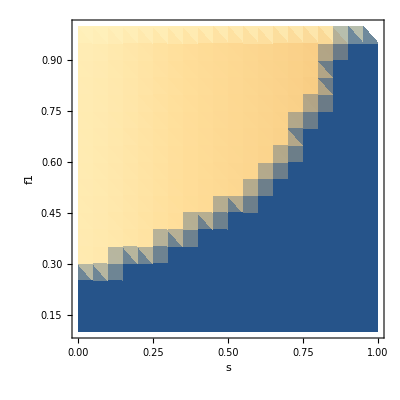

```mathematica
ListDensityPlot[Data2,AxesLabel->{"s","f1"}]
```

Numerical Analysis of 1 locus homing

```mathematica
(*Set environmental variables*)
Loci={{"Aw","Ad"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2]
```

{{{Aw},{Aw}},{{Aw},{Ad}},{{Ad},{Aw}},{{Ad},{Ad}}}

```mathematica
(*Initial conditions*)
F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];
W=ConstantArray[1,Length[Genotypes]]; 
Assert[Length[F0]==Length[Gametes]]
Assert[Total[F0]==1](*Same indexing as genotype*)
```

```mathematica
(*List of genotype1 to genotype2*)
ConversionList={
{{{"Aw"},{"Ad"}},{{"Ad"},{"Ad"}}},
{{{"Ad"},{"Aw"}},{{"Ad"},{"Ad"}}}
};
```

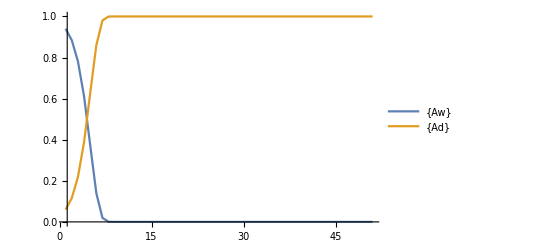

```mathematica
Clear[F]
F[t_]:=F[t]=DiploidSelection[MeioticDrive[F[t-1],MakeTransitionMatrix[ConversionList,1]]]
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,50}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->{ToString[Gametes[[1]]],ToString[Gametes[[2]]]}]
```

Numerical Analysis of 1 locus homing with resistance

## Dynamics

```mathematica
(*Set environmental variables*)
Loci={{"Aw","Ad","Ar"}};
Gametes =Tuples[Loci]
Genotypes=Tuples[Gametes,2]
```

{{Aw},{Ad},{Ar}}

{{{Aw},{Aw}},{{Aw},{Ad}},{{Aw},{Ar}},{{Ad},{Aw}},{{Ad},{Ad}},{{Ad},{Ar}},{{Ar},{Aw}},{{Ar},{Ad}},{{Ar},{Ar}}}

```mathematica
(*Initial conditions*)
(*F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];*)
F0={0.9,0.1,0};
W=ConstantArray[1,Length[Genotypes]]; 
W[[2]]=0.75;
W[[4]]=0.75;
W[[5]]=0.5;
W[[6]]=0.75;
W[[8]]=0.75;
Assert[Length[F0]==Length[Gametes]]
Assert[Total[F0]==1]
(*List of genotype1 to genotype2*)
MeioticDriveList={
{{{"Aw"},{"Ad"}},{{"Ad"},{"Ad"}},1},
{{{"Ad"},{"Aw"}},{{"Ad"},{"Ad"}},1}
};
(*List of gamete1 to gamete2*)
MutationList={
{{"Aw"},{"Ar"},0.01}
};
```

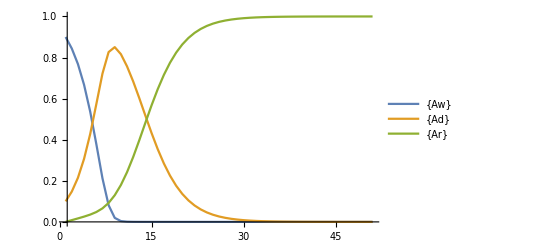

```mathematica
Clear[F]
F[t_]:=F[t]=Mutation[DiploidSelection[MeioticDrive[F[t-1],MakeTransitionMatrix[MeioticDriveList]],W,Genotypes,Gametes],MakeMutationMatrix[MutationList]]
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,50}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->{ToString[Gametes[[1]]],ToString[Gametes[[2]]],ToString[Gametes[[3]]]}]
```

Numerical Analysis of Daisy-chain homing

```mathematica
(*Set environmental variables*)
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2]
```

{{{Aw,Bw},{Aw,Bw}},{{Aw,Bw},{Aw,Bd}},{{Aw,Bw},{Ad,Bw}},{{Aw,Bw},{Ad,Bd}},{{Aw,Bd},{Aw,Bw}},{{Aw,Bd},{Aw,Bd}},{{Aw,Bd},{Ad,Bw}},{{Aw,Bd},{Ad,Bd}},{{Ad,Bw},{Aw,Bw}},{{Ad,Bw},{Aw,Bd}},{{Ad,Bw},{Ad,Bw}},{{Ad,Bw},{Ad,Bd}},{{Ad,Bd},{Aw,Bw}},{{Ad,Bd},{Aw,Bd}},{{Ad,Bd},{Ad,Bw}},{{Ad,Bd},{Ad,Bd}}}

```mathematica
(*Initial conditions*)
F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];
W=ConstantArray[1,Length[Genotypes]]; 
Assert[Length[F0]==Length[Gametes]]
Assert[Total[F0]==1](*Same indexing as genotype*)
```

```mathematica
(*List of genotype1 to genotype2*)
ConversionList={
{{{"Aw","Bw"},{"Ad","Bd"}},{{"Aw","Bd"},{"Ad","Bd"}}},
{{{"Aw","Bd"},{"Ad","Bw"}},{{"Aw","Bd"},{"Ad","Bd"}}},
{{{"Ad","Bw"},{"Aw","Bd"}},{{"Ad","Bd"},{"Aw","Bd"}}},
{{{"Ad","Bw"},{"Ad","Bd"}},{{"Ad","Bd"},{"Ad","Bd"}}},
{{{"Ad","Bd"},{"Aw","Bw"}},{{"Ad","Bd"},{"Aw","Bd"}}},
{{{"Ad","Bd"},{"Ad","Bw"}},{{"Ad","Bd"},{"Ad","Bd"}}}
};
```

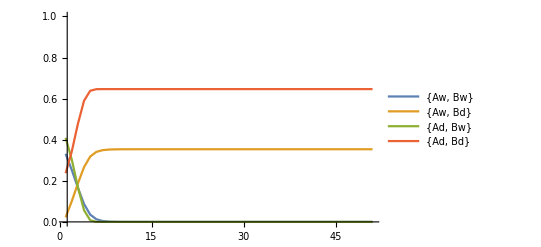

```mathematica
Clear[F]
F[t_]:=F[t]=DiploidSelection[MeioticDrive[F[t-1],MakeTransitionMatrix[ConversionList,1]]]
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,50}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->{ToString[Gametes[[1]]],ToString[Gametes[[2]]],ToString[Gametes[[3]]],ToString[Gametes[[4]]]}]
```

Numerical Analysis of 2 locus Under-dominance with homing (3 alleles)

## Dynamics

```mathematica
(*Set environmental variables*)
Loci={{"Aw","Ad","Ar"},{"Bw","Bd","Br"}};
Gametes =Tuples[Loci]
Genotypes=Tuples[Gametes,2];
```

{{Aw,Bw},{Aw,Bd},{Aw,Br},{Ad,Bw},{Ad,Bd},{Ad,Br},{Ar,Bw},{Ar,Bd},{Ar,Br}}

```mathematica
(*Initial conditions*)
F0={0.9,0,0,0,0.1,0,0,0,0};
W=ConstantArray[ϵ,Length[Genotypes]]; 
Assert[Length[F0]==Length[Gametes]]
Assert[Total[F0]==1](*Same indexing as genotype*)
```

Assert[Length[F0]==Length[Gametes]]

Assert[Total[F0]==1]

```mathematica
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],"Bd"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"],
 W[[i]]=(1-s)^(1/2);If[Count[Flatten[Genotypes[[i]]],"Ad"]==2,W[[i]]=(1-s)]
]
]
W[[1]]=1;
W[[Length[W]]]=1;
```

```mathematica
ArrayReshape[W,{9,9}]//MatrixForm
```

(1 | ϵ | ϵ | ϵ | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | √(1-s) | ϵ | ϵ | 1-s | ϵ | ϵ | √(1-s) | ϵ
√(1-s) | √(1-s) | √(1-s) | 1-s | 1-s | 1-s | √(1-s) | √(1-s) | √(1-s)
ϵ | √(1-s) | ϵ | ϵ | 1-s | ϵ | ϵ | √(1-s) | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | ϵ | ϵ | ϵ | 1)

```mathematica
Gametes
```

{{Aw,Bw},{Aw,Bd},{Aw,Br},{Ad,Bw},{Ad,Bd},{Ad,Br},{Ar,Bw},{Ar,Bd},{Ar,Br}}

```mathematica
MeioticDriveList={};
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]&&MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"],
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Aw"]->"Ad"],Position[Genotypes[[i]],"Bw"]->"Bd"],d}]];

If[MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]&&!(MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"]),
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Aw"]->"Ad"],d}]];

If[MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"]&&!(MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]),
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Bw"]->"Bd"],d}]];
]
MutationList={
{{"Aw","Bw"},{"Ar","Br"},v},
{{"Aw","Bd"},{"Ar","Bd"},v},
{{"Aw","Br"},{"Ar","Br"},v},
{{"Ad","Bw"},{"Ad","Br"},v},
{{"Ar","Bw"},{"Ar","Br"},v}
};
```

```mathematica
MutationList//MatrixForm
```

({Aw,Bw} | {Ar,Br} | v
{Aw,Bd} | {Ar,Bd} | v
{Aw,Br} | {Ar,Br} | v
{Ad,Bw} | {Ad,Br} | v
{Ar,Bw} | {Ar,Br} | v)

```mathematica
MeioticDriveList//MatrixForm;
```

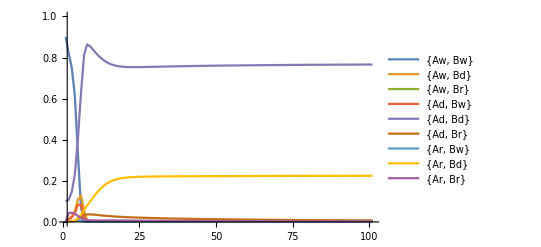

```mathematica
(*{{"Aw","Bw"},{"Aw","Bd"},{"Aw","Br"},{"Ad","Bw"},{"Ad","Bd"},{"Ad","Br"},{"Ar","Bw"},{"Ar","Bd"},{"Ar","Br"}}*)
Ws=W/.s->0.5/.ϵ->0;
MutationLists=MutationList/.v->0.05;
MeioticDriveLists=MeioticDriveList/.d->1;
Clear[F]
F[t_]:=F[t]=Mutation[DiploidSelection[MeioticDrive[Recombination[F[t-1],Gametes,Loci],MakeTransitionMatrix[MeioticDriveLists]],Ws,Genotypes,Gametes],MakeMutationMatrix[MutationLists]]
(*F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];*)
F0={0.9,0,0,0,0.1,0,0,0,0};
Assert[Total[F0]==1];
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Invasion plot

We call invasion when equilibrium {F1->1,F2->0,F3->0} is reached after 10 generations. Surely we can do a better job then this. Question: is there a way to analytically show where the threshold is (the equations are nonlinear..)

```mathematica
Clear[Finv];
Finv[t_,f1_,se_]:=Finv[t,f1,se]=Mutation[DiploidSelection[MeioticDrive[Recombination[Finv[t-1,f1,se],Gametes,Loci],MakeTransitionMatrix[MeioticDriveList]],W/.s->se,Genotypes,Gametes],MakeMutationMatrix[MutationList]]
```

```mathematica
Clear[Finv]
```

```mathematica
Equil[f1_,s_]:=Block[{out},
Finv[0,f1,s]={(1-f1),0,0,0,f1,0,0,0,0};
Finv[5,f1,s][[5]]
]
```

```mathematica
Data=Flatten[Table[{s,(1-f1),Equil[f1,s]},{s,0,1,0.05},{f1,0,1,0.05}],1];
```

Part::partw: Part 5 of Finv[5,0.,0.] does not exist.

Part::partw: Part 5 of Finv[5,0.05,0.] does not exist.

Part::partw: Part 5 of Finv[5,0.1,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListDensityPlot[Data,PlotLegends->Automatic]
```

Part::partw: Part 5 of Finv[5.,0.,0.] does not exist.

Part::partw: Part 5 of Finv[5.,0.05,0.] does not exist.

Part::partw: Part 5 of Finv[5.,0.1,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Part::partw: Part 5 of Finv[5,0.,0.] does not exist.

Part::partw: Part 5 of Finv[5,0.05,0.] does not exist.

Part::partw: Part 5 of Finv[5,0.1,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

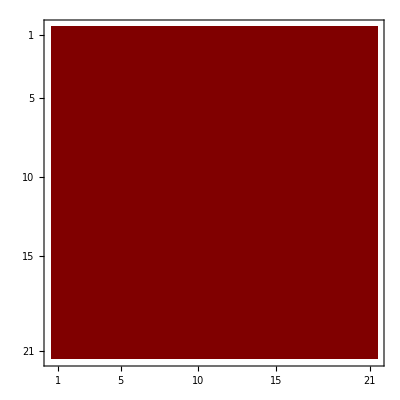

```mathematica
MatrixPlot[Table[Equil[f1,s],{s,0,1,0.05},{f1,0,1,0.05}]]
```

```mathematica
MakeMutationMatrix[MutationList].Table[1/9,{i,1,9}]/.v->0.5//Total
```

Assert::asrtf: Assertion CountDistinct[«1»]==Length[«1»] failed.

1.05556

```mathematica
v=0;
stabmat=Table[D[eqnlist[[i]],x[j]],{j,2,9},{i,2,9}]/.x[1]->1/.Table[x[i]->0,{i,2,9}]//Simplify
```

## Equilibrium

```mathematica
eq=Mutation[DiploidSelection[MeioticDrive[Recombination[Table[x[i],{i,1,9}],Gametes,Loci],MakeTransitionMatrix[MeioticDriveList]],W,Genotypes,Gametes],MakeMutationMatrix[MutationList]];
```

```mathematica
eq/.{x[1]->0,x[2]->0,x[4]->0,x[5]->0,x[6]->0,x[7]->0,x[8]->0,x[9]->0}
```

{0,0,1-v,0,0,0,0,0,v}

```mathematica
Jacobia=Table[D[eq,x[i]],{i,1,9}]
```

{1}
 |  |  |  |

```mathematica
eqJaco=Jacobia/.{x[2]->0,x[3]->0,x[4]->0,x[5]->0,x[6]->0,x[7]->0,x[8]->0,x[9]->0};
```

```mathematica
eqJaco=eqJaco/.x[1]->1//Simplify;
```

```mathematica
eqJaco//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1+d) (-1+v) ϵ | -(1+d) (-1+v) ϵ | 0 | 0 | 0 | 0 | 0 | (1+d) v ϵ | -(1+d) v ϵ
(-1+v) ϵ | 0 | ϵ-v ϵ | 0 | 0 | 0 | 0 | 0 | 0
(1+d) (-1+v) ϵ | 0 | 0 | -(1+d) (-1+v) ϵ | 0 | (1+d) v ϵ | 0 | 0 | -(1+d) v ϵ
1/2 (1+d) (-1+v) (√(1-s)+2 ϵ) | -1/2 (1+d) (-1+v) ϵ | 0 | -1/2 (1+d) (-1+v) ϵ | 1/2 (1+d) √(1-s) | 1/2 (1+d) v ϵ | 0 | 1/2 (1+d) v ϵ | -1/2 (1+d) v (√(1-s)+2 ϵ)
1/2 (3+2 d) (-1+v) ϵ | 0 | -1/2 (-1+v) ϵ | -1/2 (1+2 d) (-1+v) ϵ | 0 | 1/2 (1+v+2 d v) ϵ | 0 | 0 | -(1+d) v ϵ
(-1+v) ϵ | 0 | 0 | 0 | 0 | 0 | ϵ-v ϵ | 0 | 0
1/2 (3+2 d) (-1+v) ϵ | -1/2 (1+2 d) (-1+v) ϵ | 0 | 0 | 0 | 0 | -1/2 (-1+v) ϵ | 1/2 (1+v+2 d v) ϵ | -(1+d) v ϵ
3/2 (-1+v) ϵ | 0 | -1/2 (-1+v) ϵ | 0 | 0 | 0 | -1/2 (-1+v) ϵ | 0 | 1/2 (ϵ-v ϵ))

```mathematica
Solve[Det[eqJaco-λ IdentityMatrix[9]]==0,λ]
```

{{λ→0},{λ→1/2 (√(1-s)+d √(1-s))},{λ→(1+d) ϵ},{λ→(1+d) ϵ},{λ→1/2 (ϵ-v ϵ)},{λ→1/2 (ϵ-v ϵ)},{λ→1/2 (ϵ-v ϵ)},{λ→ϵ-v ϵ},{λ→ϵ-v ϵ}}

```mathematica
Limit[λ/.Solve[Det[eqJaco-λ IdentityMatrix[9]]==0,λ],ϵ->0]
```

{0,1/2 (1+d) √(1-s),0,0,0,0,0,0,0}

Always stable.

```mathematica
1/2 (1+d) √(1-s)≤1
```

Numerical Analysis of 2 locus Under-dominance with homing (4 alleles)

## Dynamics

Here we explore a scenario where we have 2 loci with 4 alleles.
Xw = wildtype
Xr = wiltdype, resistant to drive 
Xm = mutant drive, lost ability to drive but payload is unaffected
Xd = drive with payload.

```mathematica
(*Set environmental variables*)
Loci={{"Aw","Am","Ad","Ar"},{"Bw","Bm","Bd","Br"}};
Gametes =Tuples[Loci]
Genotypes=Tuples[Gametes,2];
```

{{Aw,Bw},{Aw,Bm},{Aw,Bd},{Aw,Br},{Am,Bw},{Am,Bm},{Am,Bd},{Am,Br},{Ad,Bw},{Ad,Bm},{Ad,Bd},{Ad,Br},{Ar,Bw},{Ar,Bm},{Ar,Bd},{Ar,Br}}

```mathematica
(*Initial conditions*)

W=ConstantArray[ϵ,Length[Genotypes]]; 
Assert[Length[F0]==Length[Gametes]];
Assert[Total[F0]==1](*Same indexing as genotype*);
```

```mathematica
For[i=1,i≤Length[Genotypes],++i,
If[(MemberQ[Flatten[Genotypes[[i]]],"Bd"]||MemberQ[Flatten[Genotypes[[i]]],"Bm"])&&(MemberQ[Flatten[Genotypes[[i]]],"Ad"]||MemberQ[Flatten[Genotypes[[i]]],"Am"]),
 W[[i]]=(1-s)^(1/2);If[(Count[Flatten[Genotypes[[i]]],"Ad"]==2||Count[Flatten[Genotypes[[i]]],"Am"]==2||(MemberQ[Flatten[Genotypes[[i]]],"Ad"]&&MemberQ[Flatten[Genotypes[[i]]],"Am"])),W[[i]]=(1-s)]
]
]
W[[1]]=1;
W[[Length[W]]]=1;
```

```mathematica
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm
```

(1 | ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ | ϵ
ϵ | √(1-s) | √(1-s) | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | √(1-s) | √(1-s) | ϵ
√(1-s) | √(1-s) | √(1-s) | √(1-s) | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | √(1-s) | √(1-s) | √(1-s) | √(1-s)
√(1-s) | √(1-s) | √(1-s) | √(1-s) | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | √(1-s) | √(1-s) | √(1-s) | √(1-s)
ϵ | √(1-s) | √(1-s) | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | √(1-s) | √(1-s) | ϵ
ϵ | √(1-s) | √(1-s) | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | √(1-s) | √(1-s) | ϵ
√(1-s) | √(1-s) | √(1-s) | √(1-s) | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | √(1-s) | √(1-s) | √(1-s) | √(1-s)
√(1-s) | √(1-s) | √(1-s) | √(1-s) | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | 1-s | √(1-s) | √(1-s) | √(1-s) | √(1-s)
ϵ | √(1-s) | √(1-s) | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | 1-s | 1-s | ϵ | ϵ | √(1-s) | √(1-s) | ϵ
ϵ | ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ
ϵ | ϵ | ϵ | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | √(1-s) | √(1-s) | ϵ | ϵ | ϵ | ϵ | 1)

```mathematica
Gametes
```

{{Aw,Bw},{Aw,Bm},{Aw,Bd},{Aw,Br},{Am,Bw},{Am,Bm},{Am,Bd},{Am,Br},{Ad,Bw},{Ad,Bm},{Ad,Bd},{Ad,Br},{Ar,Bw},{Ar,Bm},{Ar,Bd},{Ar,Br}}

```mathematica
MeioticDriveList={};
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]&&MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"],
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Aw"]->"Ad"],Position[Genotypes[[i]],"Bw"]->"Bd"],d^2}]];

If[MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]&&!(MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"]),
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Aw"]->"Ad"],d}]];

If[MemberQ[Flatten[Genotypes[[i]]],"Bw"]&&MemberQ[Flatten[Genotypes[[i]]],"Bd"]&&!(MemberQ[Flatten[Genotypes[[i]]],"Aw"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"]),
AppendTo[MeioticDriveList,{Genotypes[[i]],ReplacePart[Genotypes[[i]],Position[Genotypes[[i]],"Bw"]->"Bd"],d}]];
]
```

```mathematica
MeioticDriveList//MatrixForm;
```

```mathematica
MutationList={};
For[i=1,i≤Length[Gametes],++i,
If[MemberQ[Gametes[[i]],"Aw"],
AppendTo[MutationList,{Gametes[[i]],ReplacePart[Gametes[[i]],Position[Gametes[[i]],"Aw"]->"Ar"],v1}]];
If[MemberQ[Gametes[[i]],"Bw"],
AppendTo[MutationList,{Gametes[[i]],ReplacePart[Gametes[[i]],Position[Gametes[[i]],"Bw"]->"Br"],v1}]];
If[MemberQ[Gametes[[i]],"Ad"],
AppendTo[MutationList,{Gametes[[i]],ReplacePart[Gametes[[i]],Position[Gametes[[i]],"Ad"]->"Am"],v2}]];
If[MemberQ[Gametes[[i]],"Bd"],
AppendTo[MutationList,{Gametes[[i]],ReplacePart[Gametes[[i]],Position[Gametes[[i]],"Bd"]->"Bm"],v2}]];
]
```

```mathematica
MutationList//MatrixForm
```

({Aw,Bw} | {Ar,Bw} | v1
{Aw,Bw} | {Aw,Br} | v1
{Aw,Bm} | {Ar,Bm} | v1
{Aw,Bd} | {Ar,Bd} | v1
{Aw,Bd} | {Aw,Bm} | v2
{Aw,Br} | {Ar,Br} | v1
{Am,Bw} | {Am,Br} | v1
{Am,Bd} | {Am,Bm} | v2
{Ad,Bw} | {Ad,Br} | v1
{Ad,Bw} | {Am,Bw} | v2
{Ad,Bm} | {Am,Bm} | v2
{Ad,Bd} | {Am,Bd} | v2
{Ad,Bd} | {Ad,Bm} | v2
{Ad,Br} | {Am,Br} | v2
{Ar,Bw} | {Ar,Br} | v1
{Ar,Bd} | {Ar,Bm} | v2)

```mathematica
MeioticDriveList//MatrixForm;
```

```mathematica
MakeMutationMatrix[MutationLists]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Gametes
```

{{Aw,Bw},{Aw,Bm},{Aw,Bd},{Aw,Br},{Am,Bw},{Am,Bm},{Am,Bd},{Am,Br},{Ad,Bw},{Ad,Bm},{Ad,Bd},{Ad,Br},{Ar,Bw},{Ar,Bm},{Ar,Bd},{Ar,Br}}

### Example no drive

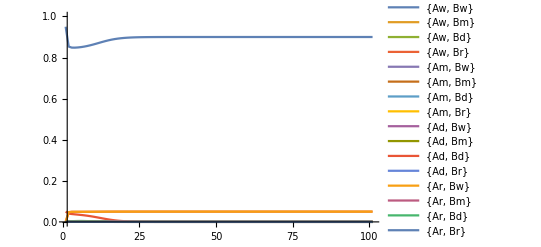

```mathematica
Ws=W/.s->0.5/.ϵ->0;
MutationLists=MutationList/.v1->0.05/.v2->0.05;
MeioticDriveLists=MeioticDriveList/.d->1;
Clear[F]
F[t_]:=F[t]=Mutation[DiploidSelection[MeioticDrive[Recombination[F[t-1],Gametes,Loci],MakeTransitionMatrix[MeioticDriveLists]],Ws,Genotypes,Gametes],MakeMutationMatrix[MutationLists]]
(*F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];*)
F0={0.95,0,0,0,0,0,0,0,0,0,.05,0,0,0,0,0};
Assert[Total[F0]==1];
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

### Example drive

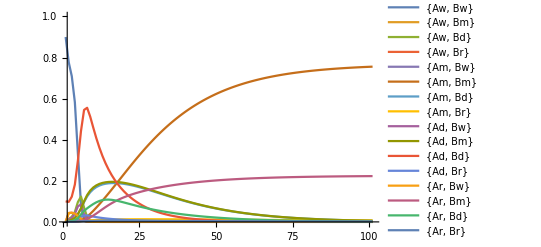

```mathematica
Ws=W/.s->0.5/.ϵ->0;
MutationLists=MutationList/.v1->0.05/.v2->0.05;
MeioticDriveLists=MeioticDriveList/.d->1;
Clear[F]
F[t_]:=F[t]=Mutation[DiploidSelection[MeioticDrive[Recombination[F[t-1],Gametes,Loci],MakeTransitionMatrix[MeioticDriveLists]],Ws,Genotypes,Gametes],MakeMutationMatrix[MutationLists]]
(*F0=Table[RandomReal[1],{i,Length[Gametes]}];
F0=F0/Total[F0];*)
F0={0.9,0,0,0,0,0,0,0,0,0,.1,0,0,0,0,0};
Assert[Total[F0]==1];
F[0]=F0;
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
Table[F[t],{t,0,100}][[100]]//Chop
```

{0,0,0,0,0,0.755003,0.00554146,0.007173,0,0.00562424,0.0000410485,0.0000534316,0,0.222795,0.00163517,0.00213371}

```mathematica
Max[Table[F[t],{t,0,100}]]
```

0.9

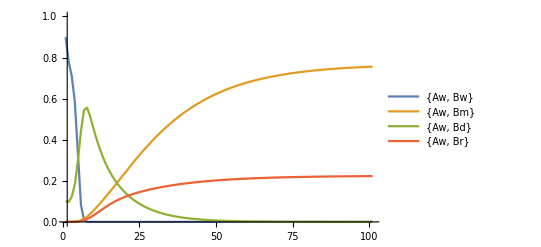

```mathematica
ListLinePlot[SubsetData[0.2,Table[F[t],{t,0,100}],Gametes],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Equilibria

```mathematica
eq=Mutation[DiploidSelection[MeioticDrive[Recombination[Table[x[i],{i,1,Length[Gametes]}],Gametes,Loci],MakeTransitionMatrix[MeioticDriveList]],W,Genotypes,Gametes],MakeMutationMatrix[MutationList]];
```

```mathematica
eq/.Table[x[i]->0,{i,1,Length[Gametes]}][[2;;]]
```

{1-2 v1,0,0,v1,0,0,0,0,0,0,0,0,v1,0,0,0}